# El molino de agua

Ecuaciones generales:



Soluciones de equilibrio:

```mathematica
Solve[{σ*(y-x)==0,r*x-y-x*z==0,x*y-b*z==0},{x,y,z}]
```

{{x→0,y→0,z→0},{x→-√(-1+r),y→-√(-1+r),z→-1+r},{x→√(-1+r),y→√(-1+r),z→-1+r}}

Matriz Jacobiana:

```mathematica
J=({{D[σ*(y-x),x], D[σ*(y-x),y], D[σ*(y-x),z]}, {D[r*x-y-x*z,x], D[r*x-y-x*z,y], D[r*x-y-x*z,z]}, {D[x*y-b*z,x], D[x*y-b*z,y], D[x*y-b*z,z]}})
```

{{-σ,σ,0},{r-z,-1,-x},{y,x,-b}}

Eigenvalores en el origen:

```mathematica
FullSimplify[Eigenvalues[J/.{x->0,y->0,z->0}]]
```

{-b,1/2 (-1-σ-√(1+σ (-2+4 r+σ))),1/2 (-1-σ+√(1+σ (-2+4 r+σ)))}

Eigenvalores en los otros puntos de equilibrio:

```mathematica
Eigenvalues[J/.{x->-√(-1+r),y->-√(-1+r),z->-1+r}]
```

{Root[-2 σ+2 r σ+(-1+b+r+b σ) #1+(1+b+σ) #1^2+#1^3&,1],Root[-2 σ+2 r σ+(-1+b+r+b σ) #1+(1+b+σ) #1^2+#1^3&,2],Root[-2 σ+2 r σ+(-1+b+r+b σ) #1+(1+b+σ) #1^2+#1^3&,3]}

Vemos numéricamente como son los eigenvalores cerca del punto de bifurcación:

```mathematica
b=1;
σ=10;
```

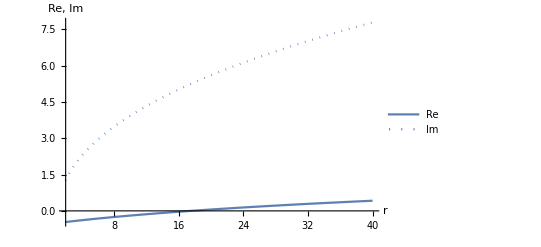

```mathematica
ReImPlot[Eigenvalues[J/.{x->-√(-1+r),y->-√(-1+r),z->-1+r}][[2]],{r,2,40},AxesLabel->{r, "Re, Im"},PlotLegends->"ReIm"]
```

Soluciones después de la bifurcación de Hopf:

```mathematica
b=8/3;
σ=10;
r=28;
```

```mathematica
sol1=NDSolve[{x'[t]==σ*(y[t]-x[t]),y'[t]==r*x[t]-y[t]-x[t]*z[t],z'[t]==x[t]*y[t]-b*z[t],x[0]==0,y[0]==1,z[0]==1},{x,y,z},{t,0,500}];
```

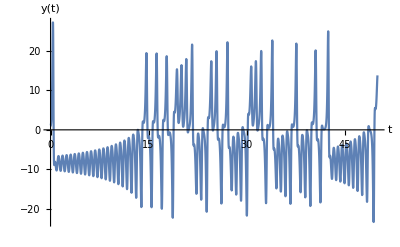

```mathematica
Plot[Evaluate[y[t]/.sol1],{t,0,50},AxesLabel->{t,y[t]}]
```

```mathematica
ParametricPlot3D[Evaluate[{x[t],y[t],z[t]}/.sol1],{t,0,100},AxesLabel->{x,y,z},PlotPoints->100,MaxRecursion->10,PlotStyle->Thin]
```

-Graphics3D-

Examinamos varias condiciones iniciales muy cerca una de otra:

```mathematica
sols=Table[NDSolve[{x'[t]==σ*(y[t]-x[t]),y'[t]==r*x[t]-y[t]-x[t]*z[t],z'[t]==x[t]*y[t]-b*z[t],x[0]==0+RandomReal[{0,0.0001}],y[0]==1+RandomReal[{0,0.0001}],z[0]==1+RandomReal[{0,0.0001}]},{x,y,z},{t,0,100}],{j,5}];
```

```mathematica
ParametricPlot3D[{Evaluate[{x[t],y[t],z[t]}/.sols[[1]]],Evaluate[{x[t],y[t],z[t]}/.sols[[2]]],Evaluate[{x[t],y[t],z[t]}/.sols[[3]]],Evaluate[{x[t],y[t],z[t]}/.sols[[4]]],Evaluate[{x[t],y[t],z[t]}/.sols[[5]]]},{t,0,100},AxesLabel->{x,y,z},PlotPoints->100,MaxRecursion->10,PlotStyle->Thin]
```

-Graphics3D-

Observemos sólo un par de ellas:

```mathematica
ParametricPlot3D[{Evaluate[{x[t],y[t],z[t]}/.sols[[1]]],Evaluate[{x[t],y[t],z[t]}/.sols[[2]]]},{t,0,100},AxesLabel->{x,y,z},PlotPoints->100,MaxRecursion->10,PlotStyle->Thin]
```

-Graphics3D-

Y sólo una de las componentes:

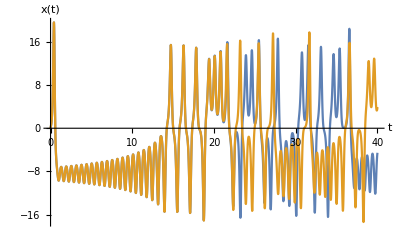

```mathematica
Plot[{Evaluate[x[t]/.sols[[1]]],Evaluate[x[t]/.sols[[2]]]},{t,0,40},AxesLabel->{t,x[t]}]
```

Y ahora grafiquemos las distancias entre ambas mientras aumenta el tiempo:

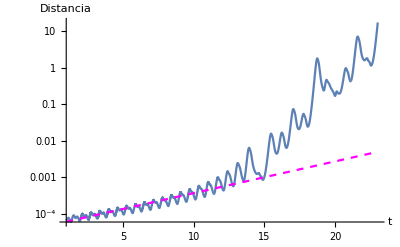

```mathematica
Show[{LogPlot[Sqrt[(Evaluate[x[t]/.sols[[1]]]-Evaluate[x[t]/.sols[[2]]])^2+(Evaluate[y[t]/.sols[[1]]]-Evaluate[y[t]/.sols[[2]]])^2+(Evaluate[z[t]/.sols[[1]]]-Evaluate[z[t]/.sols[[2]]])^2],{t,1,23},AxesLabel->{t,"Distancia"},PlotPoints->100,MaxRecursion->10,PlotRange->All],LogPlot[0.00005*Exp[0.2*t],{t,1,23},PlotStyle->{Magenta,Dashed}]}]
```

Por último, veamos como se relaciona la altura de cada máximo con la del siguiente máximo:

```mathematica
data=Reap[NDSolve[{x'[t]==σ*(y[t]-x[t]),y'[t]==x[t]*(r-z[t])-y[t],z'[t]==x[t]*y[t]-b*z[t],x[0]==0,y[0]==1,z[0]==1,WhenEvent[x[t]*y[t]-b*z[t]==0&&y[t]*σ*(y[t]-x[t])+x[t]*(x[t]*(r-z[t])-y[t])<0,Sow[z[t]]]},{x,y},{t,500,1000},MaxSteps->∞]][[-1,1]];
```

```mathematica
Dimensions[data]
```

{1334}

```mathematica
dataref=Table[{data[[i]],data[[i+1]]},{i,1333}];
```

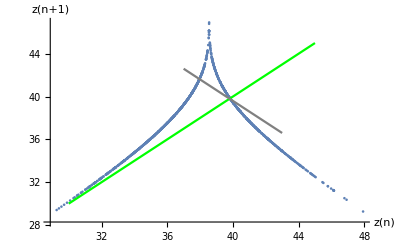

```mathematica
Show[ListPlot[dataref,AxesLabel->{z[n],z[n+1]}],Plot[x,{x,30,45},PlotStyle->Green],Plot[-x+2*39.8,{x,37,43},PlotStyle->Gray]]
```

Caos falso antes de la bifurcación:

```mathematica
sol2=NDSolve[{x'[t]==10*(y[t]-x[t]),y'[t]==21*x[t]-y[t]-x[t]*z[t],z'[t]==x[t]*y[t]-(8/3)*z[t],x[0]==3,y[0]==10,z[0]==7},{x,y,z},{t,0,500}];
```

```mathematica
ParametricPlot3D[Evaluate[{x[t],y[t],z[t]}/.sol2],{t,0,500},AxesLabel->{x,y,z},PlotPoints->100,MaxRecursion->10,PlotStyle->Thin,PlotRange->All]
```

-Graphics3D-

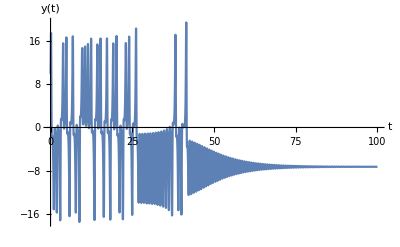

```mathematica
Plot[Evaluate[y[t]/.sol2],{t,0,100},AxesLabel->{t,y[t]},PlotRange->All]
```